```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Initial Params*)
Directory[]
```

C:\Users\Sarah Chastain\Documents

```mathematica
SetDirectory["C:\\Users\\Sarah Chastain\\transients-simulations"]
```

/home/sarah/transients-simulations

```mathematica
params = Import["./python36/config.ini","Ini"]
```

<|INITIAL PARAMETERS→<|n_sources → 2e6  ,fl_min → 5e-5,fl_max → 5   ,flux_err → 1e-1  ,dmin → 5e-3 ,dmax → 5e4    ,det_threshold → 5 ,extra_threshold → 3  ,file → output   ,lightcurvetype → gaussian |>,SIM→<|nobs → 46 ,obssens → 31.7e-6 ,obssig → 4.6e-6 ,obsinterval → 7,obsdurations → 0.009 |>|>

```mathematica
startexec = DateObject[];
nsources = ToExpression[StringReplace[params[[1]][[1]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxmin =ToExpression[StringReplace[params[[1]][[2]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxmax =ToExpression[StringReplace[params[[1]][[3]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxerr =ToExpression[StringReplace[params[[1]][[4]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
dmin =ToExpression[StringReplace[params[[1]][[5]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
dmax = ToExpression[StringReplace[params[[1]][[6]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
detThreshold = ToExpression[StringReplace[params[[1]][[7]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
extraThreshold =ToExpression[StringReplace[params[[1]][[8]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
file = StringDelete[params[[1]][[9]]," "];
transientType =StringDelete[params[[1]][[10]]," "];
nobs =ToExpression[StringReplace[params[[2]][[1]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obssens=ToExpression[StringReplace[params[[2]][[2]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obssig=ToExpression[StringReplace[params[[2]][[3]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obsinterval=ToExpression[StringReplace[params[[2]][[4]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obsdur = ToExpression[StringReplace[params[[2]][[5]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
```

```mathematica
(*Simulate Observations*)
(*start, dur, sensitivity. in Days and Jy.Choice of Gaussian and its characteristics were arbitrary.*)
obs =Table[{UnixTime[]/(60*60*24)+i*obsinterval //N,obsdur,RandomVariate[NormalDistribution[obssens,obssig]]*detThreshold},{i,1,nobs}];
```

```mathematica
obs[[1;;3]]
```

{{18239.7,0.009,0.000202134},{18246.7,0.009,0.000167164},{18253.7,0.009,0.000162692}}

```mathematica
stats = Import["./python36/"<>file<>"_"<>transientType<>"_Stat"][[2;; , 1;;3]];
gaps = Table[obs[[i+1,1]]-obs[[i,1]]+obs[[i,2]],{i,1,Length[obs]-1}];
durmax = obs[[Length[obs],1]]+obs[[Length[obs],2]]-obs[[1,1]];
sensmaxgaps=obs[[Flatten[Position[gaps,n_/;n==Max[gaps]]]+1,3]][[1]];
durmaxfred[x_]:=(((1.+fluxerr)*obs[[Length[obs],3]]*obs[[1,2]])/x)/(ⅇ^(-(durmax-obs[[1,2]]+x)/x)-ⅇ^(-((durmax+x)/x)));
maxdistfred[x_]:=(((1.+fluxerr)*sensmaxgaps*obs[[1,2]])/x)/(ⅇ^(-Max[gaps]/x)-ⅇ^(-((Max[gaps]+obs[[1,2]])/x)));
If[transientType == "tophat", gridlines = {{obs[[1,2]],durmax,Max[gaps] },{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
If[transientType == "fred", gridlines = {{obs[[1,2]]},{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
If[(transientType ≠"fred") && (transientType≠"tophat"),gridlines = {{durmax,Max[gaps]},{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
```

{{315.009,7.009},{0.000097121,0.000224793,0.000359668}}

```mathematica
gausscdf [x_,t_]:=x/6.0*√(π/2)*CDF[NormalDistribution[ x/2,x/6 ],t]
durmaxgauss[x_]:=((1.+fluxerr)*obs[[Length[obs],3]])/(gausscdf[x,durmax+x]-gausscdf[x,durmax-obs[[1,2]]+x]);
maxdistgauss[x_]:=((1.+fluxerr)*sensmaxgaps)/(gausscdf[x,Max[gaps]+obs[[1,2]]]-gausscdf[x,Max[gaps]]);
```

```mathematica
durmaxgauss[10^2]
```

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
linesgauss=LogLogPlot[-100*durmaxgauss[x],{x,5*10^1,10^5},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
ListPointPlot3D[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic}]
```

-Graphics3D-

```mathematica
durmaxgauss[10^3]
maxdistgauss[10^3]
```

7705.06

3.24493

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

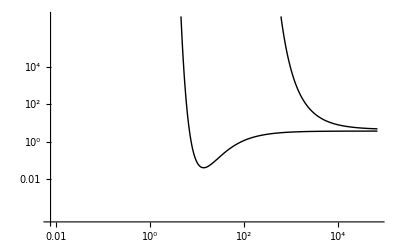

```mathematica
Plot[{durmaxgauss[x],maxdistgauss[x]},{x,Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],10^6*Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black],ScalingFunctions->{"Log10","Log10"}]
```

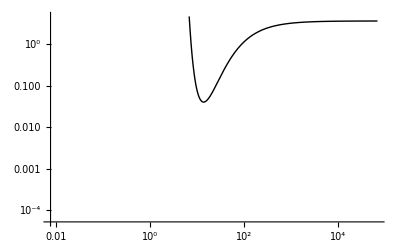

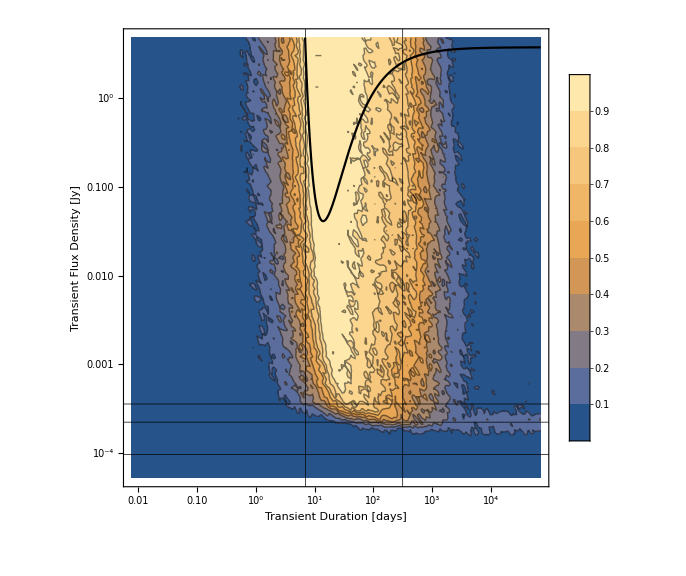

```mathematica
lines = Quiet[Plot[{durmaxgauss[x],maxdistgauss[x]},{x,Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black],ScalingFunctions->{"Log10","Log10"}]]
plotted = If[transientType =="tophat",ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},ImageSize->Large],ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},Epilog->lines[[1]],ImageSize->Large]]
```

```mathematica
Export[transientType<>"_lightcurve.pdf",plotted]
```

gaussian_lightcurve.pdf

```mathematica
-durmaxgauss[50]
```

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

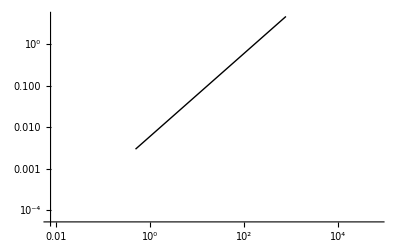

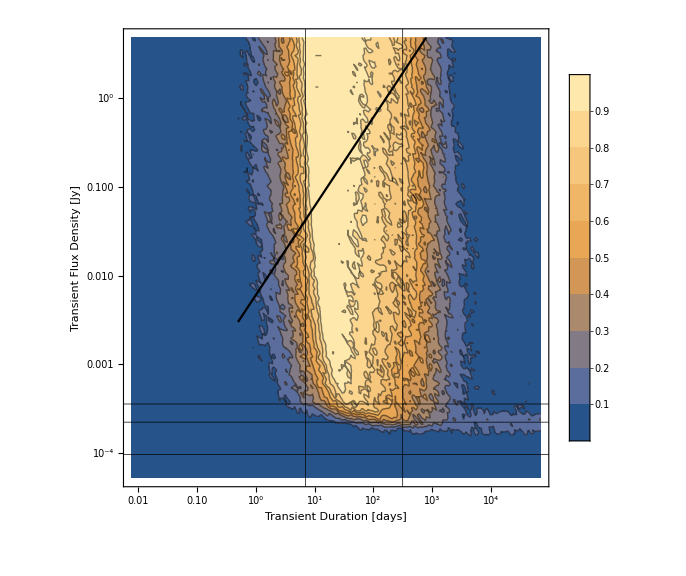

```mathematica
linesgauss=Plot[0.006 x^1,{x,0.5,10^8},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black],ScalingFunctions->{"Log10","Log10"}]
Show[ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},ImageSize->Large,PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]},{0,1.0}}],linesgauss]
```

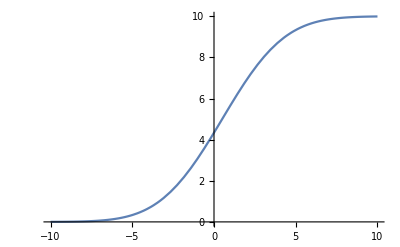

```mathematica
Plot[10*CDF[NormalDistribution[0+0.5, 0.5*6],x],{x,-10,10}]
```

```mathematica
obs[[1,1]]
```

18239.7

```mathematica
10*CDF[NormalDistribution[0+0.5, 0.5*6],8]-10*CDF[NormalDistribution[0+0.5, 0.5*6],4]
```

1.15463

```mathematica
Solve[ⅇ^-2*f/(√(2*π*τ^2))==f]
```

{{f→0},{τ→-1/(ⅇ^2 √(2 π))},{τ→1/(ⅇ^2 √(2 π))}}

```mathematica
ⅇ^-2*1/(√(2*π))
```

1/(ⅇ^2 √(2 π))

```mathematica
N[1/(ⅇ^2 √(2 π))]
```

0.053991

```mathematica
Integrate[F0*tobs*√(2*π)*PDF[NormalDistribution[Tburst + τ/2,τ/6 ],t],t]
```

-F0 √(π/2) tobs Erf[(3 (-2 t+2 Tburst+τ))/(√2 τ)]

```mathematica
PDF[NormalDistribution[μ,σ],t]
```

(ⅇ^(-(t-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
CDF[NormalDistribution[Tburst + τ/2,τ/6 ],t]
```

1/2 Erfc[(3 √2 (-t+Tburst+τ/2))/τ]

```mathematica
durmaxfred[x_]:=((1.+fluxerr)*obs[[Length[obs],3]]*obs[[1,2]])/(x*(ⅇ^(-(durmax-obs[[1,2]]+x)/x)-ⅇ^(-((durmax+x)/x))));
maxdistfred[x_]:=((1.+fluxerr)*sensmaxgaps*obs[[1,2]])/(x*(ⅇ^(-Max[gaps]/x)-ⅇ^(-((Max[gaps]+obs[[1,2]])/x))));
```

```mathematica
Integrate[ F0*ⅇ^(-t/τ),τ,Assumptions->t>0&&τ>0]
```

F0 (ⅇ^(-t/τ) τ+t ExpIntegralEi[-t/τ])

```mathematica
gaussianLightcurveInstantaneous[t_,τ_,F0_,tobs_,Tburst_]:=F0*tobs*√(2*π)*PDF[NormalDistribution[Tburst + τ/2,τ/6 ],t]
```

```mathematica
Integrate[gaussianLightcurveInstantaneous[y, x,F,tobs,0] ,y]
```

-F √(π/2) tobs Erf[(3 (x-2 y))/(√2 x)]

```mathematica
F[τ] √(π/2) tobs Erf[(3 (-2 (durmax-obs[[1,2]]+x)+τ))/(√2 τ)]-F[τ] √(π/2) tobs Erf[(3 (-2 t+τ))/(√2 τ)]==Fobs tobs
```

-√(π/2) tobs Erf[(3 (-2 t+τ))/(√2 τ)] F[τ]+√(π/2) tobs Erf[(3 (-2 (315.+x)+τ))/(√2 τ)] F[τ]==Fobs tobs